```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/rex

```mathematica
hbar=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
cijTh=10^-12;
numRAD=7;
epsi=1;
dbg=False;
```

ℏ^2/(2  μ) = 20.7369

Read LEC list (e.g. fitted to two-body scattering length via <<<Fit_Scattering_length.nb>>>)

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
(*LECsNUCL=Import["../LECs_nucl_Rimas-Martin.dat","Table"];
activeLEC=LECsNUCL[[All,{1,2}]][[2;;]];*)
activeLEC=Import["/home/rex/LECs_lambda","Table"]
```

{{#,L[fm^-1],C_0[nucl],D_0[nucl],D_0[5],D_0[3],D_0[15],D_0[20],D_0[25],D_0[30],D_0[35],D_0[40],D_0[45],D_0[50],D_0[76]},{4,-505.15,1486.34,1750.34,1950.34,1160,975,825,698,590,493,405,327,0},{5,-623.753},{6,-741.15,2225.34,2525.34,2735.34,1825,1600},{7,-858.067},{8,-974.604,2932.34,3250.34,3480.34,2492},{9,-1090.83},{10,-1206.79,3630.34,3960.34,4190.34,3152}}

Calculate the dimer wave function in a Gaussian basis rdimer=∑_(i=1)^N c_i·e^(-α_i r^2)

```mathematica
I1=Compile[{lam,b1,b2},(Pi/(2b1+2 b2+4 lam))^(3/2)];
I3=Compile[{b1,b2},3 b1 b2 Pi^(3/2)/(2^(1/2)(b1+b2)^(5/2))];
```

```mathematica
ham=Compile[{lam,b1,b2,lec},Module[{},lec I1[lam,b1,b2]+(1/mh2) I3[b1,b2]]];
norm=Compile[{b1,b2},Module[{},(Pi/(2 b1+2 b2))^(3/2)]];
```

```mathematica
CalcDimerE[basisW_,lam_,lec_]:=
Module[{eval,evec},
Nd=Length[basisW];
hamm=Table[ham[lam,basisW[[i]],basisW[[j]],lec],{i,Nd},{j,Nd}];
normm=Table[norm[basisW[[i]],basisW[[j]]],{i,Nd},{j,Nd}];
{eval,evec}=Eigensystem[{hamm,normm}];
ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];
{eigsorted[[1]],Transpose[{vecsorted[[1]],basisW}]}
];
```

```mathematica
ApproxDimerWF[lamd_,dimD_,nbrThreads_,nbrWidthSamples_,minW_,maxW_,minWidthDiff_,verbosity_,σw_:2]:=Block[{LECc,LECd,e0,λ=lamd,Δ=minWidthDiff,αmax=maxW,αmin=minW,Nd=dimD,Ns=nbrWidthSamples,Nth=nbrThreads},

LECc=Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
LECd=Flatten[Select[activeLEC,#[[1]]==λ&]][[3]];
Print[LECc];Print[LECd];
widths={};
rndPrec=5;
Do[

widthLr=Sort[#]&/@RandomReal[{SetPrecision[αmin,rndPrec+1],SetPrecision[αmax,rndPrec+1]},{Ns,Nd},WorkingPrecision->rndPrec];

(*t1=Sort[#]&/@Abs[RandomVariate[NormalDistribution[αmin,σw],{Ns,IntegerPart[Nd/2]}]];
t2=Sort[#]&/@Abs[RandomVariate[NormalDistribution[αmax,σw],{Ns,IntegerPart[Nd/2]}]];

widthLr=ArrayReshape[Flatten[#]&/@Tuples[{t1,t2}],{Nd,Ns}];*)

widthL=Select[widthLr,AllTrue[Select[Tuples[#,2],#[[1]]!=#[[2]]&],Abs[#[[1]]-#[[2]]]>Δ&]&];

AppendTo[widths,widthL];
,{nn,Nth}];

If[verbosity==1,Print["λ = ",λ,"   C_0(λ) = ",LECc,"  #(width-set candidates) = ",Length[Flatten[widths,1]],"  in ",Nth," parallel threads."]];
opti={};
SetSharedVariable[opti];

ta=AbsoluteTime[];
ParallelDo[
widthL=widths[[nt]];
results=0.0;e0=0.0;
optSet={};
Do[
Nd=Length[wi];
hamm=Table[ham[λ,wi[[i]],wi[[j]],LECc],{i,Nd},{j,Nd}];
normm=Table[norm[wi[[i]],wi[[j]]],{i,Nd},{j,Nd}];

{eval,evec}=Eigensystem[{hamm,normm}];

ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];

If[(
(eigsorted[[1]]<results)&&
(eigsorted[[1]]>-2.65)&&
(Im[eigsorted[[1]]]==0)&&
(NormTF[Transpose[{vecsorted[[1]],wi}]]>10^-5)&&
(Min[Abs[vecsorted[[1]]]]>10^-2)&&
(ContainsOnly[Sign[vecsorted[[1]]],{1}]||ContainsOnly[Sign[vecsorted[[1]]],{-1}])
),
(*Print[eigsorted[[1]],eigsorted];*)
e0=eigsorted[[1]];
results=eigsorted[[1]];
optSet=Transpose[{vecsorted[[1]],wi}];
]
,{wi,widthL}];
If[verbosity==1,Print["Core ",nt," : ",e0,optSet]];
AppendTo[opti,{e0,optSet}];
,{nt,Nth}];
tb=AbsoluteTime[];

e0=Sort[opti][[1]][[1]];
optSet=Sort[opti][[1]][[2]];
If[verbosity==1,Print["optimum of ",Style[Length[Flatten[widths,1]],Red,Italic,18]," candidate width sets found in Δt = ",Style[tb-ta,Red,Italic,18]," sec.          : E_0 = ",e0]];
(*Print["opt. basis: ",optSet];*)
(*Put[optSet,"dimerWF_"<>ToString[e0]<>".mmo"];
Put[e0,"E0_"<>ToString[e0]<>".mmo"];*)
{e0,optSet}
];
rma=2;rmi=0.;nR=100;
rR=Range[rmi,rma,(rma-rmi)/nR];
```

```mathematica
RiccatiBesselJ=Compile[{z,l},z SphericalBesselJ[l,z]];
RiccatiBesselN=Compile[{z,l},(-1)^l z SphericalBesselY[l,z]];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha=Compile[{ra,ka,la,ha},RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]];

beta=Compile[{rb,kb,lb,hb},RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])];
```

reference: J. Spanier, K.B. Oldham - An Atlas of Functions (1987)

x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)
 to optimize runtime, we substitute in this implementation -- valid for S-wave scattering, only:
 j_0(i x)=Sinh[x]/x
 and
 j_1(i x)=i x^-1(Cosh[x]-Sinh[x]/x)
 For numerical stability at arguments x>>1, it is curucial to subsitute the following representation:
 e^(-aR^2-bR'^2) Sinh[bRR']=1/2(e^(-aR^2-bR'^2+bRR')-e^(-aR^2-bR'^2-bRR')) and similarly for the hyperbolic cosine;
 Retaining the Sinh built-in function throws, at best, warnings, and yields significantly inaccurate and almost certainly non-sensical results!

```mathematica
NormTF=Compile[{{core,_Real,2}},Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] core[[k]][[1]] core[[l]][[1]] (2)^0.5(1/((core[[i]][[2]]+core[[j]][[2]]) (core[[k]][[2]]+core[[l]][[2]])))^(3/2),{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]]];


VlocTF=Compile[{r,lam,Cc,Dd,Aa,Bb,Gg,Hh},Block[{eta1,eta2,eta3,w1,w2,w3},
eta1=(16 Cc)/(lam Bb+Gg(lam+2Bb)+lam Hh+2Bb Hh+Aa(lam+2Gg+2Hh))^(3/2);
w1=(2lam(Aa+Bb)(Gg+Hh))/(lam Bb+Gg(lam+2Bb)+lam Hh+2Bb Hh+Aa(lam+2Gg+2Hh));
eta2=(2/((lam+Aa+Bb)(lam+Gg+Hh)))^(3/2)Dd;
w2=(2lam(Aa+Bb))/(lam+Aa+Bb);
eta3=(8Dd)/((2 lam^2+lam Bb+Gg(5lam+2Bb)+5lam Hh+2Bb Hh+Aa(lam+2Gg+2Hh))^(3/2));
w3=(2lam (2lam+Aa+Bb)(Gg+Hh))/(2 lam^2+lam Bb+Gg(5lam+2Bb)+5lam Hh+2Bb Hh+Aa(lam+2Gg+2Hh));
eta1 Exp[-w1 r^2]+eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]
]];

(*WnolocTF3=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,Bb,Gg,Hh,Ll,TwoMyOverHBsq,radMA},Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3,Sinh1,Sinh2,Sinh3,CoshA,numRAD=radMA},
zeta1=-(π^(3/2)/(√2))/(Aa+Bb+Gg+ Hh)^(3/2) (1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=-(π^(3/2)/(√2)) Cc/(2lam+Aa +Bb+ Gg+Hh)^(3/2);
zeta3=-(π^(3/2)/(√2)) Cc/(2lam+Aa +Bb+ Gg+Hh)^(3/2);

a2=(4Hh(2lam+Bb)+Gg(2lam +Bb+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b2=(Gg(4 lam+2 Bb-2 Hh)+Aa (-4 lam-2 Bb+2 Hh))/(2 (2 lam+Aa+Bb+Gg+Hh));
c2=( Gg(2lam+Bb+Hh)+Aa(2lam+4Gg+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

a3= (4Bb(2lam+Hh)+Gg(Bb+2lam+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4lam-2Hh)+Aa(4lam+2Hh-2Bb))/(2(2 lam+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2lam+Hh)+Aa(4Gg+2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

(* these conditions avoid having to multiply a Gaussian whose argument is larger than that of a Sinc with the
latter which amounts only to a numerical zero; if we assume any number <= 10^-14 to be zero, numRAD ≈ 217 *)

(*SinhA=If[((b1!=0.0)&&(Abs[b1 r rp]<0.1 Abs[a1 r^2+c1 rp^2])&&(Abs[a1 r^2+c1 rp^2]<numRAD)),Exp[-a1 r^2-c1 rp^2] Sinh[b1 r rp]/b1,0.0];
SinhB=If[((b2!=0.0)&&(Abs[b2 r rp]<0.1 Abs[a2 r^2+c2 rp^2])&&(Abs[a2 r^2+c2 rp^2]<numRAD)),Exp[-a2 r^2-c2 rp^2] Sinh[b2 r rp]/b2,0.0];
SinhC=If[((b3!=0.0)&&(Abs[b3 r rp]<0.1 Abs[a3 r^2+c3 rp^2])&&(Abs[a3 r^2+c3 rp^2]<numRAD)),Exp[-a3 r^2-c3 rp^2] Sinh[b3 r rp]/b3,0.0];
CoshA=If[((Abs[b1 r rp]<0.1 Abs[a1 r^2+c1 rp^2])&&(Abs[a1 r^2+c1 rp^2]<numRAD)),Exp[-a1 r^2-c1 rp^2] Cosh[b1 r rp],0.0];*)
Sinh1=If[b1==0,0,(Exp[b1 r rp-a1 r^2-c1 rp^2]-Exp[-b1 r rp-a1 r^2-c1 rp^2])/(2 b1)];
Sinh2=If[b2==0,0,(Exp[b2 r rp-a2 r^2-c2 rp^2]-Exp[-b2 r rp-a2 r^2-c2 rp^2])/(2 b2)];
Sinh3=If[b3==0,0,(Exp[b3 r rp-a3 r^2-c3 rp^2]-Exp[-b3 r rp-a3 r^2-c3 rp^2])/(2 b3)];

-(4 Pi) (zeta1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) Sinh1-4 a1 Sqrt[3]^-1 (-0.5 r rp (Exp[b1 r rp-a1 r^2-c1 rp^2]+Exp[-b1 r rp-a1 r^2-c1 rp^2])+Sinh1))+zeta2 Sinh2+zeta3 Sinh3)

(*SinhA=If[b1==0.0,0.0,(Exp[-a1 r^2-c1 rp^2+b1 r rp]-Exp[-a1 r^2-c1 rp^2-b1 r rp])/(2 b1)];
SinhB=If[b2==0.0,0.0,(Exp[-a2 r^2-c2 rp^2+b2 r rp]-Exp[-a2 r^2-c2 rp^2-b2 r rp])/(2 b2)];
SinhC=If[b3==0.0,0.0,(Exp[-a3 r^2-c3 rp^2+b3 r rp]-Exp[-a3 r^2-c3 rp^2-b3 r rp])/(2 b3)];
CoshA=0.5 (Exp[-a1 r^2-c1 rp^2+b1 r rp]+Exp[-a1 r^2-c1 rp^2+b1 r rp]);*)

(*-(4 Pi) (zeta1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) SinhA-4 a1 Sqrt[3]^-1 (-r rp CoshA+SinhB))+zeta2 SinhB+zeta3 SinhC)*)
(*Chop[Exp[-a3 r^2-c3 rp^2] SinhC,10^-10]*)
]];*)
(*WnolocTF3=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,Bb,Gg,Hh,Ll,TwoMyOverHBsq},Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(*-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5*)-2Pi^1.5/(2(Aa+Bb+Gg+ Hh))^(3/2) (1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=(*-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5*)-2 Pi^1.5 Cc/(2(2lam+Aa +Bb+ Gg+Hh))^(3/2);
zeta3=(*-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5*)-2 Pi^1.5 Cc/(2(2lam+Aa +Bb+ Gg+Hh))^(3/2);

a2=(4Hh(2lam+Bb)+Gg(2lam+Bb+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b2=(Gg(4 lam+2 Bb-2 Hh)+Aa (-4 lam-2 Bb+2 Hh))/(2 (2 lam+Aa+Bb+Gg+Hh));
c2=( Gg(2lam+Bb+Hh)+Aa(2lam+4Gg+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

a3= (4Bb(2lam+Hh)+Gg(Bb+2lam+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4lam-2Hh)+Aa(4lam+2Hh-2Bb))/(2(2 lam+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2lam+Hh)+Aa(4Gg+2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

Sinh1=(Exp[b1 r rp-a1 r^2-c1 rp^2]-Exp[-b1 r rp-a1 r^2-c1 rp^2])/(2 b1+100 $MachineEpsilon);
Sinh2=(Exp[b2 r rp-a2 r^2-c2 rp^2]-Exp[-b2 r rp-a2 r^2-c2 rp^2])/(2 b2+100 $MachineEpsilon);
Sinh3=(Exp[b3 r rp-a3 r^2-c3 rp^2]-Exp[-b3 r rp-a3 r^2-c3 rp^2])/(2 b3+100 $MachineEpsilon);

-(4 Pi) (zeta1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) Sinh1-4 a1 Sqrt[3]^-1 (-0.5 r rp (Exp[b1 r rp-a1 r^2-c1 rp^2]+Exp[-b1 r rp-a1 r^2-c1 rp^2])+Sinh1))+zeta2 Sinh2+zeta3 Sinh3)
]];*)
```

```mathematica
SolveSecularP3[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ,numR_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
t1=AbsoluteTime[];
hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1/NormTF[a00];

(*Wmat=ConstantArray[0,{Npoints,Npoints}];*)

Wmats={};
SetSharedVariable[Wmats];

ParallelDo[

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]];

(*wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF3[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]],Lin,TwoMyOverHBsq,numR],{i,1,Npoints},{j,1,Npoints}(*,ProgressReporting->False*)]; *)
AppendTo[Wmats,cij (amat(*+wmat*))];

,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmats];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);
t2=AbsoluteTime[];
Print["finite-difference runtime Δt = ",(t2-t1)/60.," mins     p_match·r_max = ",momentum Rdis];
{tanDelta,usol}
];
```

```mathematica
GetEREP3[l_,rMax_,nPoints_,core_,LECc_,LECd_,energ_:0.001,numR_]:=Module[{locall=l},

momFM=Sqrt[mh2 energ];
(*TanDelSwave=SolveSecular[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
TanDelSwave*){-2.20461,{{-0.00558396,0.050935},{-0.0146543,0.21000},{-0.0406902,0.99319},{-0.691399,6.2469},{0.706724,6.7867},{-0.143551,10.734}}};
{TanDelSwave,wfkt}=SolveSecularP3[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2,numR];
{-TanDelSwave/Sqrt[mh2 energ ],wfkt}
]
```

-741.15

2225.34

λ = 6   C_0(λ) = -741.15  #(width-set candidates) = 39832  in 4 parallel threads.

Core 4 : -1.76413{{0.136524,0.074428},{0.527787,0.98832},{0.629075,5.168},{0.554137,10.807}}

Core 2 : -1.53822{{0.185768,0.18897},{0.341769,0.89423},{0.863635,5.248},{0.320653,18.073}}

Core 3 : -2.02776{{-0.1389,0.097072},{-0.374827,0.82541},{-0.625474,3.5587},{-0.67007,12.415}}

Core 1 : -1.7873{{-0.142719,0.090476},{-0.361363,0.91203},{-0.55704,3.0843},{-0.733999,12.911}}

optimum of 39832 candidate width sets found in Δt = 10.80741 sec.          : E_0 = -2.02776

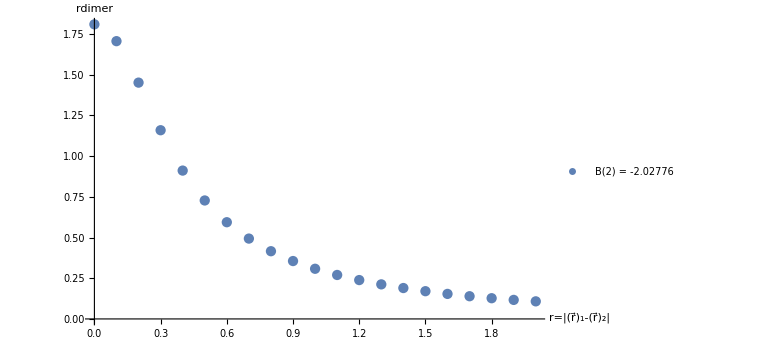

```mathematica
flag=1;

lambdaTest=6;
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
dCores={};
(*WS={4.3584650 ,  2.8802200 ,  2.0651530  , 1.6563710  , 1.1615310  , 0.8261400,0.5922700  , 0.4901080 ,  0.3227900   ,0.2522220  , 0.1357500};
dCores={CalcDimerE[WS,lambdaTest,LECc]}*)

ncc=1;
If[flag>0,
Do[
{eDi,wDi}=ApproxDimerWF[lambdaTest,4,4,10000,0.001,Random[Real,{15,35}],0.01,1,2];
AppendTo[dCores,{eDi,wDi}];
,{nc,Range[ncc]}];
];

If[flag>=0,
NormTF[#]&/@dCores[[All,2]];

dCores=CalcDimerE[dCores[[#]][[2]][[All,2]],lambdaTest,LECc]&/@Range[Length[dCores]];

JacobiTrailWavefunctionU=Total[Abs[#[[1]]] Exp[-#[[2]] r1^2]&/@#[[2]]]&/@dCores;rR=Range[0,2,0.100];
JacobiTrailWavefunctionDataU=Table[#/.{r1->R1},{R1,rR}]&/@JacobiTrailWavefunctionU;

plotData=Transpose[{rR,#}]&/@JacobiTrailWavefunctionDataU;

lgd="B(2) = "<>ToString[#[[1]]]&/@dCores;
ListPlot[plotData,PlotRange->Full,AxesLabel->{"r=|(r⃗)_1-(r⃗)_2|","TemplateBox[{\"r\", \"dimer\"},\"BraKet\"]"},PlotLegends->lgd,ImageSize->Large]
]
```

```mathematica
(* energy at which the scattering length is obtained from the amplitude *)
energ=0.001;
(* Integration grid *)
rMa=12;
grdPerFermi=15;
nGrd=IntegerPart[rMa grdPerFermi];
results={};
(*dCores=Get["dimerCores_"<>ToString[lambdaTest]<>".dat"];*)
nbrOfCores=Length[dCores];

Do[
{e0Core,dimerCore}=dCores[[nn]];

dimCore=Length[dimerCore];

tmp=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,LECd,energ,numRAD][[1]];
AppendTo[results,{lambdaTest,LECc,rMa,nGrd,e0Core,dimCore,tmp,tmp/(hbar/√(Mm Abs[e0Core]))}];
Print["core ",nn,"| maxE=",numRAD," )  λ=",lambdaTest," ; C_0(λ)=",LECc," ; R_max=",rMa," ; #=",nGrd," ; E_match=",energ," ; B(2)=",e0Core," ; dim_d=",dimCore," ; a_dd=",tmp," ; a_dd/a_aa=",tmp/(hbar/√(Mm Abs[e0Core]))];
,{nn,Length[dCores]},{numRAD,{1}}];
```

Set::shape: Lists {TanDelSwave,wfkt} and SolveSecularP3[12,180,0.0069443,0,6,-741.15,LECd,{{-0.1389,0.097072},{-0.374827,0.82541},{-0.625474,3.5587},{-0.67007,12.415}},0.0482233,1] are not the same shape.

core 1| maxE=1 )  λ=6 ; C_0(λ)=-741.15 ; R_max=12 ; #=180 ; E_match=0.001 ; B(2)=-2.02776 ; dim_d=4 ; a_dd=-144.003 TanDelSwave ; a_dd/a_aa=-31.8415 TanDelSwave

### maximal-integration-range dependence of the a_dd scattering-length pre/post-diction

20.7369

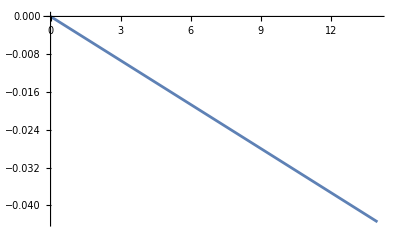

```mathematica
1/mh2
momFM=Sqrt[mh2 0.0002];
Plot[RiccatiBesselJ[momFM r,0]/RiccatiBesselN[momFM r,0](*-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin])*),{r,0,14}]
```

```mathematica
lambdaTest=4;
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]]
(*LECd=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[14]]*)
LECd=-5000
```

-505.15

-5000

0.871831

finite-difference runtime Δt = 0.0179816 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -170     R_max = 12     #(grid points) = 144                a_dd = 0.991153 fm        a_dd/a_aa = 0.223972

finite-difference runtime Δt = 0.0175816 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -171     R_max = 12     #(grid points) = 144                a_dd = 0.990323 fm        a_dd/a_aa = 0.223785

finite-difference runtime Δt = 0.0170659 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -172     R_max = 12     #(grid points) = 144                a_dd = 0.989493 fm        a_dd/a_aa = 0.223597

finite-difference runtime Δt = 0.0170694 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -173     R_max = 12     #(grid points) = 144                a_dd = 0.988663 fm        a_dd/a_aa = 0.22341

finite-difference runtime Δt = 0.0179573 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -174     R_max = 12     #(grid points) = 144                a_dd = 0.987832 fm        a_dd/a_aa = 0.223222

finite-difference runtime Δt = 0.0170886 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -175     R_max = 12     #(grid points) = 144                a_dd = 0.987001 fm        a_dd/a_aa = 0.223034

finite-difference runtime Δt = 0.0178707 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -176     R_max = 12     #(grid points) = 144                a_dd = 0.986171 fm        a_dd/a_aa = 0.222847

finite-difference runtime Δt = 0.0174681 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -177     R_max = 12     #(grid points) = 144                a_dd = 0.98534 fm        a_dd/a_aa = 0.222659

finite-difference runtime Δt = 0.0173951 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -178     R_max = 12     #(grid points) = 144                a_dd = 0.984509 fm        a_dd/a_aa = 0.222471

finite-difference runtime Δt = 0.0175184 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -179     R_max = 12     #(grid points) = 144                a_dd = 0.983678 fm        a_dd/a_aa = 0.222283

finite-difference runtime Δt = 0.0166454 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -180     R_max = 12     #(grid points) = 144                a_dd = 0.982846 fm        a_dd/a_aa = 0.222095

finite-difference runtime Δt = 0.0166085 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -181     R_max = 12     #(grid points) = 144                a_dd = 0.982015 fm        a_dd/a_aa = 0.221907

finite-difference runtime Δt = 0.0173518 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -182     R_max = 12     #(grid points) = 144                a_dd = 0.981184 fm        a_dd/a_aa = 0.22172

finite-difference runtime Δt = 0.0172607 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -183     R_max = 12     #(grid points) = 144                a_dd = 0.980352 fm        a_dd/a_aa = 0.221532

finite-difference runtime Δt = 0.0181849 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -184     R_max = 12     #(grid points) = 144                a_dd = 0.97952 fm        a_dd/a_aa = 0.221344

finite-difference runtime Δt = 0.0170166 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -185     R_max = 12     #(grid points) = 144                a_dd = 0.978688 fm        a_dd/a_aa = 0.221156

finite-difference runtime Δt = 0.0180269 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -186     R_max = 12     #(grid points) = 144                a_dd = 0.977856 fm        a_dd/a_aa = 0.220968

finite-difference runtime Δt = 0.0173379 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -187     R_max = 12     #(grid points) = 144                a_dd = 0.977024 fm        a_dd/a_aa = 0.22078

finite-difference runtime Δt = 0.0166519 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -188     R_max = 12     #(grid points) = 144                a_dd = 0.976192 fm        a_dd/a_aa = 0.220592

finite-difference runtime Δt = 0.0168584 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -189     R_max = 12     #(grid points) = 144                a_dd = 0.975359 fm        a_dd/a_aa = 0.220403

finite-difference runtime Δt = 0.0168501 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -190     R_max = 12     #(grid points) = 144                a_dd = 0.974527 fm        a_dd/a_aa = 0.220215

finite-difference runtime Δt = 0.0171167 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -191     R_max = 12     #(grid points) = 144                a_dd = 0.973694 fm        a_dd/a_aa = 0.220027

finite-difference runtime Δt = 0.0173333 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -192     R_max = 12     #(grid points) = 144                a_dd = 0.972862 fm        a_dd/a_aa = 0.219839

finite-difference runtime Δt = 0.0185849 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -193     R_max = 12     #(grid points) = 144                a_dd = 0.972029 fm        a_dd/a_aa = 0.219651

finite-difference runtime Δt = 0.018233 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -194     R_max = 12     #(grid points) = 144                a_dd = 0.971196 fm        a_dd/a_aa = 0.219463

finite-difference runtime Δt = 0.0182981 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -195     R_max = 12     #(grid points) = 144                a_dd = 0.970362 fm        a_dd/a_aa = 0.219274

finite-difference runtime Δt = 0.0170307 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -196     R_max = 12     #(grid points) = 144                a_dd = 0.969529 fm        a_dd/a_aa = 0.219086

finite-difference runtime Δt = 0.0174296 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -197     R_max = 12     #(grid points) = 144                a_dd = 0.968696 fm        a_dd/a_aa = 0.218898

finite-difference runtime Δt = 0.0180445 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -198     R_max = 12     #(grid points) = 144                a_dd = 0.967862 fm        a_dd/a_aa = 0.218709

finite-difference runtime Δt = 0.0176347 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -199     R_max = 12     #(grid points) = 144                a_dd = 0.967028 fm        a_dd/a_aa = 0.218521

finite-difference runtime Δt = 0.0167441 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -200     R_max = 12     #(grid points) = 144                a_dd = 0.966195 fm        a_dd/a_aa = 0.218332

finite-difference runtime Δt = 0.0169232 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -201     R_max = 12     #(grid points) = 144                a_dd = 0.965361 fm        a_dd/a_aa = 0.218144

finite-difference runtime Δt = 0.0172588 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -202     R_max = 12     #(grid points) = 144                a_dd = 0.964527 fm        a_dd/a_aa = 0.217956

finite-difference runtime Δt = 0.0168181 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -203     R_max = 12     #(grid points) = 144                a_dd = 0.963692 fm        a_dd/a_aa = 0.217767

finite-difference runtime Δt = 0.0178965 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -204     R_max = 12     #(grid points) = 144                a_dd = 0.962858 fm        a_dd/a_aa = 0.217578

finite-difference runtime Δt = 0.0180714 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -205     R_max = 12     #(grid points) = 144                a_dd = 0.962023 fm        a_dd/a_aa = 0.21739

finite-difference runtime Δt = 0.0180521 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -206     R_max = 12     #(grid points) = 144                a_dd = 0.961189 fm        a_dd/a_aa = 0.217201

finite-difference runtime Δt = 0.0171277 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -207     R_max = 12     #(grid points) = 144                a_dd = 0.960354 fm        a_dd/a_aa = 0.217013

finite-difference runtime Δt = 0.017774 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -208     R_max = 12     #(grid points) = 144                a_dd = 0.959519 fm        a_dd/a_aa = 0.216824

finite-difference runtime Δt = 0.0177252 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -209     R_max = 12     #(grid points) = 144                a_dd = 0.958684 fm        a_dd/a_aa = 0.216635

finite-difference runtime Δt = 0.0172118 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -210     R_max = 12     #(grid points) = 144                a_dd = 0.957849 fm        a_dd/a_aa = 0.216447

finite-difference runtime Δt = 0.0164809 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -211     R_max = 12     #(grid points) = 144                a_dd = 0.957014 fm        a_dd/a_aa = 0.216258

finite-difference runtime Δt = 0.0167888 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -212     R_max = 12     #(grid points) = 144                a_dd = 0.956178 fm        a_dd/a_aa = 0.216069

finite-difference runtime Δt = 0.0179774 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -213     R_max = 12     #(grid points) = 144                a_dd = 0.955343 fm        a_dd/a_aa = 0.21588

finite-difference runtime Δt = 0.0175954 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -214     R_max = 12     #(grid points) = 144                a_dd = 0.954507 fm        a_dd/a_aa = 0.215691

finite-difference runtime Δt = 0.0176509 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -215     R_max = 12     #(grid points) = 144                a_dd = 0.953671 fm        a_dd/a_aa = 0.215503

finite-difference runtime Δt = 0.0173466 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -216     R_max = 12     #(grid points) = 144                a_dd = 0.952835 fm        a_dd/a_aa = 0.215314

finite-difference runtime Δt = 0.0169886 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -217     R_max = 12     #(grid points) = 144                a_dd = 0.951999 fm        a_dd/a_aa = 0.215125

finite-difference runtime Δt = 0.0180638 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -218     R_max = 12     #(grid points) = 144                a_dd = 0.951163 fm        a_dd/a_aa = 0.214936

finite-difference runtime Δt = 0.0170126 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -219     R_max = 12     #(grid points) = 144                a_dd = 0.950326 fm        a_dd/a_aa = 0.214747

finite-difference runtime Δt = 0.0169474 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -220     R_max = 12     #(grid points) = 144                a_dd = 0.94949 fm        a_dd/a_aa = 0.214558

finite-difference runtime Δt = 0.0169269 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -221     R_max = 12     #(grid points) = 144                a_dd = 0.948653 fm        a_dd/a_aa = 0.214369

finite-difference runtime Δt = 0.0173594 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -222     R_max = 12     #(grid points) = 144                a_dd = 0.947816 fm        a_dd/a_aa = 0.21418

finite-difference runtime Δt = 0.0166339 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -223     R_max = 12     #(grid points) = 144                a_dd = 0.94698 fm        a_dd/a_aa = 0.21399

finite-difference runtime Δt = 0.0187196 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -224     R_max = 12     #(grid points) = 144                a_dd = 0.946142 fm        a_dd/a_aa = 0.213801

finite-difference runtime Δt = 0.0172718 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -225     R_max = 12     #(grid points) = 144                a_dd = 0.945305 fm        a_dd/a_aa = 0.213612

finite-difference runtime Δt = 0.0174494 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -226     R_max = 12     #(grid points) = 144                a_dd = 0.944468 fm        a_dd/a_aa = 0.213423

finite-difference runtime Δt = 0.0162308 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -227     R_max = 12     #(grid points) = 144                a_dd = 0.94363 fm        a_dd/a_aa = 0.213234

finite-difference runtime Δt = 0.0178273 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -228     R_max = 12     #(grid points) = 144                a_dd = 0.942793 fm        a_dd/a_aa = 0.213044

finite-difference runtime Δt = 0.0179474 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -229     R_max = 12     #(grid points) = 144                a_dd = 0.941955 fm        a_dd/a_aa = 0.212855

finite-difference runtime Δt = 0.0169315 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -230     R_max = 12     #(grid points) = 144                a_dd = 0.941117 fm        a_dd/a_aa = 0.212666

finite-difference runtime Δt = 0.0165388 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -231     R_max = 12     #(grid points) = 144                a_dd = 0.940279 fm        a_dd/a_aa = 0.212476

finite-difference runtime Δt = 0.0169587 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -232     R_max = 12     #(grid points) = 144                a_dd = 0.939441 fm        a_dd/a_aa = 0.212287

finite-difference runtime Δt = 0.017626 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -233     R_max = 12     #(grid points) = 144                a_dd = 0.938603 fm        a_dd/a_aa = 0.212097

finite-difference runtime Δt = 0.0184399 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -234     R_max = 12     #(grid points) = 144                a_dd = 0.937764 fm        a_dd/a_aa = 0.211908

finite-difference runtime Δt = 0.0181347 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -235     R_max = 12     #(grid points) = 144                a_dd = 0.936925 fm        a_dd/a_aa = 0.211718

finite-difference runtime Δt = 0.0175125 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -236     R_max = 12     #(grid points) = 144                a_dd = 0.936087 fm        a_dd/a_aa = 0.211529

finite-difference runtime Δt = 0.0172935 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -237     R_max = 12     #(grid points) = 144                a_dd = 0.935248 fm        a_dd/a_aa = 0.211339

finite-difference runtime Δt = 0.0178245 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -238     R_max = 12     #(grid points) = 144                a_dd = 0.934409 fm        a_dd/a_aa = 0.21115

finite-difference runtime Δt = 0.0173712 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -239     R_max = 12     #(grid points) = 144                a_dd = 0.933569 fm        a_dd/a_aa = 0.21096

finite-difference runtime Δt = 0.0180804 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -240     R_max = 12     #(grid points) = 144                a_dd = 0.93273 fm        a_dd/a_aa = 0.21077

finite-difference runtime Δt = 0.0178668 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -241     R_max = 12     #(grid points) = 144                a_dd = 0.931891 fm        a_dd/a_aa = 0.210581

finite-difference runtime Δt = 0.018296 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -242     R_max = 12     #(grid points) = 144                a_dd = 0.931051 fm        a_dd/a_aa = 0.210391

finite-difference runtime Δt = 0.0174917 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -243     R_max = 12     #(grid points) = 144                a_dd = 0.930211 fm        a_dd/a_aa = 0.210201

finite-difference runtime Δt = 0.0175211 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -244     R_max = 12     #(grid points) = 144                a_dd = 0.929371 fm        a_dd/a_aa = 0.210011

finite-difference runtime Δt = 0.0167879 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -245     R_max = 12     #(grid points) = 144                a_dd = 0.928531 fm        a_dd/a_aa = 0.209822

finite-difference runtime Δt = 0.0169683 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -246     R_max = 12     #(grid points) = 144                a_dd = 0.927691 fm        a_dd/a_aa = 0.209632

finite-difference runtime Δt = 0.0182933 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -247     R_max = 12     #(grid points) = 144                a_dd = 0.926851 fm        a_dd/a_aa = 0.209442

finite-difference runtime Δt = 0.0170451 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -248     R_max = 12     #(grid points) = 144                a_dd = 0.92601 fm        a_dd/a_aa = 0.209252

finite-difference runtime Δt = 0.0181614 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -249     R_max = 12     #(grid points) = 144                a_dd = 0.92517 fm        a_dd/a_aa = 0.209062

finite-difference runtime Δt = 0.0173905 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -250     R_max = 12     #(grid points) = 144                a_dd = 0.924329 fm        a_dd/a_aa = 0.208872

finite-difference runtime Δt = 0.0176518 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -251     R_max = 12     #(grid points) = 144                a_dd = 0.923488 fm        a_dd/a_aa = 0.208682

finite-difference runtime Δt = 0.0177552 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -252     R_max = 12     #(grid points) = 144                a_dd = 0.922647 fm        a_dd/a_aa = 0.208492

finite-difference runtime Δt = 0.0172464 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -253     R_max = 12     #(grid points) = 144                a_dd = 0.921806 fm        a_dd/a_aa = 0.208302

finite-difference runtime Δt = 0.0177351 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -254     R_max = 12     #(grid points) = 144                a_dd = 0.920964 fm        a_dd/a_aa = 0.208112

finite-difference runtime Δt = 0.0186166 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -255     R_max = 12     #(grid points) = 144                a_dd = 0.920123 fm        a_dd/a_aa = 0.207922

finite-difference runtime Δt = 0.0175034 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -256     R_max = 12     #(grid points) = 144                a_dd = 0.919281 fm        a_dd/a_aa = 0.207731

finite-difference runtime Δt = 0.0180881 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -257     R_max = 12     #(grid points) = 144                a_dd = 0.918439 fm        a_dd/a_aa = 0.207541

finite-difference runtime Δt = 0.0175772 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -258     R_max = 12     #(grid points) = 144                a_dd = 0.917597 fm        a_dd/a_aa = 0.207351

finite-difference runtime Δt = 0.0182321 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -259     R_max = 12     #(grid points) = 144                a_dd = 0.916755 fm        a_dd/a_aa = 0.207161

finite-difference runtime Δt = 0.0170877 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -260     R_max = 12     #(grid points) = 144                a_dd = 0.915913 fm        a_dd/a_aa = 0.20697

finite-difference runtime Δt = 0.0183937 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -261     R_max = 12     #(grid points) = 144                a_dd = 0.91507 fm        a_dd/a_aa = 0.20678

finite-difference runtime Δt = 0.0184081 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -262     R_max = 12     #(grid points) = 144                a_dd = 0.914228 fm        a_dd/a_aa = 0.206589

finite-difference runtime Δt = 0.0174799 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -263     R_max = 12     #(grid points) = 144                a_dd = 0.913385 fm        a_dd/a_aa = 0.206399

finite-difference runtime Δt = 0.0178031 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -264     R_max = 12     #(grid points) = 144                a_dd = 0.912542 fm        a_dd/a_aa = 0.206209

finite-difference runtime Δt = 0.017948 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -265     R_max = 12     #(grid points) = 144                a_dd = 0.911699 fm        a_dd/a_aa = 0.206018

finite-difference runtime Δt = 0.0171484 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -266     R_max = 12     #(grid points) = 144                a_dd = 0.910856 fm        a_dd/a_aa = 0.205828

finite-difference runtime Δt = 0.0166721 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -267     R_max = 12     #(grid points) = 144                a_dd = 0.910013 fm        a_dd/a_aa = 0.205637

finite-difference runtime Δt = 0.0170533 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -268     R_max = 12     #(grid points) = 144                a_dd = 0.909169 fm        a_dd/a_aa = 0.205446

finite-difference runtime Δt = 0.017264 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -269     R_max = 12     #(grid points) = 144                a_dd = 0.908326 fm        a_dd/a_aa = 0.205256

finite-difference runtime Δt = 0.0173374 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -270     R_max = 12     #(grid points) = 144                a_dd = 0.907482 fm        a_dd/a_aa = 0.205065

finite-difference runtime Δt = 0.0172123 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -271     R_max = 12     #(grid points) = 144                a_dd = 0.906638 fm        a_dd/a_aa = 0.204874

finite-difference runtime Δt = 0.0174726 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -272     R_max = 12     #(grid points) = 144                a_dd = 0.905794 fm        a_dd/a_aa = 0.204684

finite-difference runtime Δt = 0.0169358 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -273     R_max = 12     #(grid points) = 144                a_dd = 0.904949 fm        a_dd/a_aa = 0.204493

finite-difference runtime Δt = 0.0185643 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -274     R_max = 12     #(grid points) = 144                a_dd = 0.904105 fm        a_dd/a_aa = 0.204302

finite-difference runtime Δt = 0.0171474 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -275     R_max = 12     #(grid points) = 144                a_dd = 0.90326 fm        a_dd/a_aa = 0.204111

finite-difference runtime Δt = 0.0168548 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -276     R_max = 12     #(grid points) = 144                a_dd = 0.902416 fm        a_dd/a_aa = 0.20392

finite-difference runtime Δt = 0.0165348 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -277     R_max = 12     #(grid points) = 144                a_dd = 0.901571 fm        a_dd/a_aa = 0.203729

finite-difference runtime Δt = 0.0182104 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -278     R_max = 12     #(grid points) = 144                a_dd = 0.900726 fm        a_dd/a_aa = 0.203538

finite-difference runtime Δt = 0.0175368 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -279     R_max = 12     #(grid points) = 144                a_dd = 0.899881 fm        a_dd/a_aa = 0.203347

finite-difference runtime Δt = 0.0181264 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -280     R_max = 12     #(grid points) = 144                a_dd = 0.899035 fm        a_dd/a_aa = 0.203156

finite-difference runtime Δt = 0.0172584 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -281     R_max = 12     #(grid points) = 144                a_dd = 0.89819 fm        a_dd/a_aa = 0.202965

finite-difference runtime Δt = 0.0168565 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -282     R_max = 12     #(grid points) = 144                a_dd = 0.897344 fm        a_dd/a_aa = 0.202774

finite-difference runtime Δt = 0.0179155 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -283     R_max = 12     #(grid points) = 144                a_dd = 0.896498 fm        a_dd/a_aa = 0.202583

finite-difference runtime Δt = 0.0173683 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -284     R_max = 12     #(grid points) = 144                a_dd = 0.895652 fm        a_dd/a_aa = 0.202392

finite-difference runtime Δt = 0.0176598 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -285     R_max = 12     #(grid points) = 144                a_dd = 0.894806 fm        a_dd/a_aa = 0.202201

finite-difference runtime Δt = 0.0174317 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -286     R_max = 12     #(grid points) = 144                a_dd = 0.89396 fm        a_dd/a_aa = 0.20201

finite-difference runtime Δt = 0.0176618 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -287     R_max = 12     #(grid points) = 144                a_dd = 0.893114 fm        a_dd/a_aa = 0.201818

finite-difference runtime Δt = 0.018393 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -288     R_max = 12     #(grid points) = 144                a_dd = 0.892267 fm        a_dd/a_aa = 0.201627

finite-difference runtime Δt = 0.018071 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -289     R_max = 12     #(grid points) = 144                a_dd = 0.89142 fm        a_dd/a_aa = 0.201436

finite-difference runtime Δt = 0.0182048 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -290     R_max = 12     #(grid points) = 144                a_dd = 0.890573 fm        a_dd/a_aa = 0.201244

finite-difference runtime Δt = 0.0181576 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -291     R_max = 12     #(grid points) = 144                a_dd = 0.889726 fm        a_dd/a_aa = 0.201053

finite-difference runtime Δt = 0.0174124 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -292     R_max = 12     #(grid points) = 144                a_dd = 0.888879 fm        a_dd/a_aa = 0.200861

finite-difference runtime Δt = 0.0185217 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -293     R_max = 12     #(grid points) = 144                a_dd = 0.888032 fm        a_dd/a_aa = 0.20067

finite-difference runtime Δt = 0.0175755 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -294     R_max = 12     #(grid points) = 144                a_dd = 0.887184 fm        a_dd/a_aa = 0.200478

finite-difference runtime Δt = 0.0177931 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -295     R_max = 12     #(grid points) = 144                a_dd = 0.886336 fm        a_dd/a_aa = 0.200287

finite-difference runtime Δt = 0.0173247 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -296     R_max = 12     #(grid points) = 144                a_dd = 0.885488 fm        a_dd/a_aa = 0.200095

finite-difference runtime Δt = 0.0181518 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -297     R_max = 12     #(grid points) = 144                a_dd = 0.88464 fm        a_dd/a_aa = 0.199904

finite-difference runtime Δt = 0.0173896 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -298     R_max = 12     #(grid points) = 144                a_dd = 0.883792 fm        a_dd/a_aa = 0.199712

finite-difference runtime Δt = 0.0174622 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -299     R_max = 12     #(grid points) = 144                a_dd = 0.882944 fm        a_dd/a_aa = 0.19952

finite-difference runtime Δt = 0.0177839 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -300     R_max = 12     #(grid points) = 144                a_dd = 0.882095 fm        a_dd/a_aa = 0.199328

finite-difference runtime Δt = 0.0179974 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -301     R_max = 12     #(grid points) = 144                a_dd = 0.881247 fm        a_dd/a_aa = 0.199137

finite-difference runtime Δt = 0.0174535 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -302     R_max = 12     #(grid points) = 144                a_dd = 0.880398 fm        a_dd/a_aa = 0.198945

finite-difference runtime Δt = 0.0180435 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -303     R_max = 12     #(grid points) = 144                a_dd = 0.879549 fm        a_dd/a_aa = 0.198753

finite-difference runtime Δt = 0.0176241 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -304     R_max = 12     #(grid points) = 144                a_dd = 0.8787 fm        a_dd/a_aa = 0.198561

finite-difference runtime Δt = 0.0172689 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -305     R_max = 12     #(grid points) = 144                a_dd = 0.87785 fm        a_dd/a_aa = 0.198369

finite-difference runtime Δt = 0.0175092 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -306     R_max = 12     #(grid points) = 144                a_dd = 0.877001 fm        a_dd/a_aa = 0.198177

finite-difference runtime Δt = 0.0176996 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -307     R_max = 12     #(grid points) = 144                a_dd = 0.876151 fm        a_dd/a_aa = 0.197985

finite-difference runtime Δt = 0.0173543 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -308     R_max = 12     #(grid points) = 144                a_dd = 0.875301 fm        a_dd/a_aa = 0.197793

finite-difference runtime Δt = 0.0169854 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -309     R_max = 12     #(grid points) = 144                a_dd = 0.874451 fm        a_dd/a_aa = 0.197601

finite-difference runtime Δt = 0.0173723 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -310     R_max = 12     #(grid points) = 144                a_dd = 0.873601 fm        a_dd/a_aa = 0.197409

finite-difference runtime Δt = 0.0174951 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -311     R_max = 12     #(grid points) = 144                a_dd = 0.872751 fm        a_dd/a_aa = 0.197217

finite-difference runtime Δt = 0.0170265 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -312     R_max = 12     #(grid points) = 144                a_dd = 0.8719 fm        a_dd/a_aa = 0.197025

finite-difference runtime Δt = 0.0170307 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -313     R_max = 12     #(grid points) = 144                a_dd = 0.87105 fm        a_dd/a_aa = 0.196832

finite-difference runtime Δt = 0.0176686 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -314     R_max = 12     #(grid points) = 144                a_dd = 0.870199 fm        a_dd/a_aa = 0.19664

finite-difference runtime Δt = 0.0170422 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -315     R_max = 12     #(grid points) = 144                a_dd = 0.869348 fm        a_dd/a_aa = 0.196448

finite-difference runtime Δt = 0.0169843 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -316     R_max = 12     #(grid points) = 144                a_dd = 0.868497 fm        a_dd/a_aa = 0.196256

finite-difference runtime Δt = 0.0168691 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -317     R_max = 12     #(grid points) = 144                a_dd = 0.867645 fm        a_dd/a_aa = 0.196063

finite-difference runtime Δt = 0.016465 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -318     R_max = 12     #(grid points) = 144                a_dd = 0.866794 fm        a_dd/a_aa = 0.195871

finite-difference runtime Δt = 0.0174905 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -319     R_max = 12     #(grid points) = 144                a_dd = 0.865942 fm        a_dd/a_aa = 0.195678

finite-difference runtime Δt = 0.0170955 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -320     R_max = 12     #(grid points) = 144                a_dd = 0.86509 fm        a_dd/a_aa = 0.195486

finite-difference runtime Δt = 0.0173168 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -321     R_max = 12     #(grid points) = 144                a_dd = 0.864238 fm        a_dd/a_aa = 0.195293

finite-difference runtime Δt = 0.0182859 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -322     R_max = 12     #(grid points) = 144                a_dd = 0.863386 fm        a_dd/a_aa = 0.195101

finite-difference runtime Δt = 0.0180994 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -323     R_max = 12     #(grid points) = 144                a_dd = 0.862534 fm        a_dd/a_aa = 0.194908

finite-difference runtime Δt = 0.0182481 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -324     R_max = 12     #(grid points) = 144                a_dd = 0.861681 fm        a_dd/a_aa = 0.194715

finite-difference runtime Δt = 0.0172035 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -325     R_max = 12     #(grid points) = 144                a_dd = 0.860829 fm        a_dd/a_aa = 0.194523

finite-difference runtime Δt = 0.0174228 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -326     R_max = 12     #(grid points) = 144                a_dd = 0.859976 fm        a_dd/a_aa = 0.19433

finite-difference runtime Δt = 0.0174596 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -327     R_max = 12     #(grid points) = 144                a_dd = 0.859123 fm        a_dd/a_aa = 0.194137

finite-difference runtime Δt = 0.0177654 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -328     R_max = 12     #(grid points) = 144                a_dd = 0.85827 fm        a_dd/a_aa = 0.193944

finite-difference runtime Δt = 0.0174858 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -329     R_max = 12     #(grid points) = 144                a_dd = 0.857416 fm        a_dd/a_aa = 0.193752

finite-difference runtime Δt = 0.0173548 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -330     R_max = 12     #(grid points) = 144                a_dd = 0.856563 fm        a_dd/a_aa = 0.193559

finite-difference runtime Δt = 0.0173649 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -331     R_max = 12     #(grid points) = 144                a_dd = 0.855709 fm        a_dd/a_aa = 0.193366

finite-difference runtime Δt = 0.0170928 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -332     R_max = 12     #(grid points) = 144                a_dd = 0.854855 fm        a_dd/a_aa = 0.193173

finite-difference runtime Δt = 0.0176953 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -333     R_max = 12     #(grid points) = 144                a_dd = 0.854001 fm        a_dd/a_aa = 0.19298

finite-difference runtime Δt = 0.0166146 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -334     R_max = 12     #(grid points) = 144                a_dd = 0.853147 fm        a_dd/a_aa = 0.192787

finite-difference runtime Δt = 0.016989 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -335     R_max = 12     #(grid points) = 144                a_dd = 0.852292 fm        a_dd/a_aa = 0.192594

finite-difference runtime Δt = 0.0172355 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -336     R_max = 12     #(grid points) = 144                a_dd = 0.851438 fm        a_dd/a_aa = 0.192401

finite-difference runtime Δt = 0.0177996 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -337     R_max = 12     #(grid points) = 144                a_dd = 0.850583 fm        a_dd/a_aa = 0.192208

finite-difference runtime Δt = 0.0171479 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -338     R_max = 12     #(grid points) = 144                a_dd = 0.849728 fm        a_dd/a_aa = 0.192014

finite-difference runtime Δt = 0.0170027 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -339     R_max = 12     #(grid points) = 144                a_dd = 0.848873 fm        a_dd/a_aa = 0.191821

finite-difference runtime Δt = 0.0180982 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -340     R_max = 12     #(grid points) = 144                a_dd = 0.848018 fm        a_dd/a_aa = 0.191628

finite-difference runtime Δt = 0.0179561 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -341     R_max = 12     #(grid points) = 144                a_dd = 0.847162 fm        a_dd/a_aa = 0.191435

finite-difference runtime Δt = 0.0170209 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -342     R_max = 12     #(grid points) = 144                a_dd = 0.846307 fm        a_dd/a_aa = 0.191241

finite-difference runtime Δt = 0.0173603 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -343     R_max = 12     #(grid points) = 144                a_dd = 0.845451 fm        a_dd/a_aa = 0.191048

finite-difference runtime Δt = 0.0185621 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -344     R_max = 12     #(grid points) = 144                a_dd = 0.844595 fm        a_dd/a_aa = 0.190854

finite-difference runtime Δt = 0.0184944 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -345     R_max = 12     #(grid points) = 144                a_dd = 0.843739 fm        a_dd/a_aa = 0.190661

finite-difference runtime Δt = 0.0181269 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -346     R_max = 12     #(grid points) = 144                a_dd = 0.842882 fm        a_dd/a_aa = 0.190467

finite-difference runtime Δt = 0.0172108 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -347     R_max = 12     #(grid points) = 144                a_dd = 0.842026 fm        a_dd/a_aa = 0.190274

finite-difference runtime Δt = 0.0176168 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -348     R_max = 12     #(grid points) = 144                a_dd = 0.841169 fm        a_dd/a_aa = 0.19008

finite-difference runtime Δt = 0.0176412 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -349     R_max = 12     #(grid points) = 144                a_dd = 0.840312 fm        a_dd/a_aa = 0.189887

finite-difference runtime Δt = 0.0167042 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -350     R_max = 12     #(grid points) = 144                a_dd = 0.839455 fm        a_dd/a_aa = 0.189693

finite-difference runtime Δt = 0.0178007 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -351     R_max = 12     #(grid points) = 144                a_dd = 0.838598 fm        a_dd/a_aa = 0.189499

finite-difference runtime Δt = 0.0169867 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -352     R_max = 12     #(grid points) = 144                a_dd = 0.83774 fm        a_dd/a_aa = 0.189306

finite-difference runtime Δt = 0.0181241 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -353     R_max = 12     #(grid points) = 144                a_dd = 0.836883 fm        a_dd/a_aa = 0.189112

finite-difference runtime Δt = 0.0174286 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -354     R_max = 12     #(grid points) = 144                a_dd = 0.836025 fm        a_dd/a_aa = 0.188918

finite-difference runtime Δt = 0.0184655 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -355     R_max = 12     #(grid points) = 144                a_dd = 0.835167 fm        a_dd/a_aa = 0.188724

finite-difference runtime Δt = 0.0177443 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -356     R_max = 12     #(grid points) = 144                a_dd = 0.834309 fm        a_dd/a_aa = 0.18853

finite-difference runtime Δt = 0.0179561 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -357     R_max = 12     #(grid points) = 144                a_dd = 0.833451 fm        a_dd/a_aa = 0.188336

finite-difference runtime Δt = 0.018431 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -358     R_max = 12     #(grid points) = 144                a_dd = 0.832592 fm        a_dd/a_aa = 0.188142

finite-difference runtime Δt = 0.0179817 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -359     R_max = 12     #(grid points) = 144                a_dd = 0.831734 fm        a_dd/a_aa = 0.187948

finite-difference runtime Δt = 0.0181373 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -360     R_max = 12     #(grid points) = 144                a_dd = 0.830875 fm        a_dd/a_aa = 0.187754

finite-difference runtime Δt = 0.0185517 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -361     R_max = 12     #(grid points) = 144                a_dd = 0.830016 fm        a_dd/a_aa = 0.18756

finite-difference runtime Δt = 0.0183807 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -362     R_max = 12     #(grid points) = 144                a_dd = 0.829156 fm        a_dd/a_aa = 0.187366

finite-difference runtime Δt = 0.0173085 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -363     R_max = 12     #(grid points) = 144                a_dd = 0.828297 fm        a_dd/a_aa = 0.187172

finite-difference runtime Δt = 0.0188134 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -364     R_max = 12     #(grid points) = 144                a_dd = 0.827437 fm        a_dd/a_aa = 0.186977

finite-difference runtime Δt = 0.0186054 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -365     R_max = 12     #(grid points) = 144                a_dd = 0.826578 fm        a_dd/a_aa = 0.186783

finite-difference runtime Δt = 0.0179303 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -366     R_max = 12     #(grid points) = 144                a_dd = 0.825718 fm        a_dd/a_aa = 0.186589

finite-difference runtime Δt = 0.0188959 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -367     R_max = 12     #(grid points) = 144                a_dd = 0.824858 fm        a_dd/a_aa = 0.186394

finite-difference runtime Δt = 0.0183322 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -368     R_max = 12     #(grid points) = 144                a_dd = 0.823997 fm        a_dd/a_aa = 0.1862

finite-difference runtime Δt = 0.0182133 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -369     R_max = 12     #(grid points) = 144                a_dd = 0.823137 fm        a_dd/a_aa = 0.186005

finite-difference runtime Δt = 0.0179916 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -370     R_max = 12     #(grid points) = 144                a_dd = 0.822276 fm        a_dd/a_aa = 0.185811

finite-difference runtime Δt = 0.0180056 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -371     R_max = 12     #(grid points) = 144                a_dd = 0.821415 fm        a_dd/a_aa = 0.185616

finite-difference runtime Δt = 0.017467 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -372     R_max = 12     #(grid points) = 144                a_dd = 0.820554 fm        a_dd/a_aa = 0.185422

finite-difference runtime Δt = 0.0184991 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -373     R_max = 12     #(grid points) = 144                a_dd = 0.819693 fm        a_dd/a_aa = 0.185227

finite-difference runtime Δt = 0.0184039 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -374     R_max = 12     #(grid points) = 144                a_dd = 0.818831 fm        a_dd/a_aa = 0.185033

finite-difference runtime Δt = 0.0182658 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -375     R_max = 12     #(grid points) = 144                a_dd = 0.81797 fm        a_dd/a_aa = 0.184838

finite-difference runtime Δt = 0.018366 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -376     R_max = 12     #(grid points) = 144                a_dd = 0.817108 fm        a_dd/a_aa = 0.184643

finite-difference runtime Δt = 0.017469 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -377     R_max = 12     #(grid points) = 144                a_dd = 0.816246 fm        a_dd/a_aa = 0.184448

finite-difference runtime Δt = 0.0169952 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -378     R_max = 12     #(grid points) = 144                a_dd = 0.815384 fm        a_dd/a_aa = 0.184254

finite-difference runtime Δt = 0.0181658 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -379     R_max = 12     #(grid points) = 144                a_dd = 0.814521 fm        a_dd/a_aa = 0.184059

finite-difference runtime Δt = 0.0184603 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -380     R_max = 12     #(grid points) = 144                a_dd = 0.813659 fm        a_dd/a_aa = 0.183864

finite-difference runtime Δt = 0.0170607 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -381     R_max = 12     #(grid points) = 144                a_dd = 0.812796 fm        a_dd/a_aa = 0.183669

finite-difference runtime Δt = 0.0177018 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -382     R_max = 12     #(grid points) = 144                a_dd = 0.811933 fm        a_dd/a_aa = 0.183474

finite-difference runtime Δt = 0.0175997 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -383     R_max = 12     #(grid points) = 144                a_dd = 0.81107 fm        a_dd/a_aa = 0.183279

finite-difference runtime Δt = 0.017642 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -384     R_max = 12     #(grid points) = 144                a_dd = 0.810207 fm        a_dd/a_aa = 0.183084

finite-difference runtime Δt = 0.0173162 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -385     R_max = 12     #(grid points) = 144                a_dd = 0.809343 fm        a_dd/a_aa = 0.182889

finite-difference runtime Δt = 0.0178459 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -386     R_max = 12     #(grid points) = 144                a_dd = 0.80848 fm        a_dd/a_aa = 0.182693

finite-difference runtime Δt = 0.0174583 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -387     R_max = 12     #(grid points) = 144                a_dd = 0.807616 fm        a_dd/a_aa = 0.182498

finite-difference runtime Δt = 0.0185988 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -388     R_max = 12     #(grid points) = 144                a_dd = 0.806752 fm        a_dd/a_aa = 0.182303

finite-difference runtime Δt = 0.0177029 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -389     R_max = 12     #(grid points) = 144                a_dd = 0.805887 fm        a_dd/a_aa = 0.182108

finite-difference runtime Δt = 0.0183744 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -390     R_max = 12     #(grid points) = 144                a_dd = 0.805023 fm        a_dd/a_aa = 0.181912

finite-difference runtime Δt = 0.0188112 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -391     R_max = 12     #(grid points) = 144                a_dd = 0.804158 fm        a_dd/a_aa = 0.181717

finite-difference runtime Δt = 0.0183009 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -392     R_max = 12     #(grid points) = 144                a_dd = 0.803293 fm        a_dd/a_aa = 0.181521

finite-difference runtime Δt = 0.0178659 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -393     R_max = 12     #(grid points) = 144                a_dd = 0.802428 fm        a_dd/a_aa = 0.181326

finite-difference runtime Δt = 0.0178695 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -394     R_max = 12     #(grid points) = 144                a_dd = 0.801563 fm        a_dd/a_aa = 0.18113

finite-difference runtime Δt = 0.017761 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -395     R_max = 12     #(grid points) = 144                a_dd = 0.800698 fm        a_dd/a_aa = 0.180935

finite-difference runtime Δt = 0.0181563 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -396     R_max = 12     #(grid points) = 144                a_dd = 0.799832 fm        a_dd/a_aa = 0.180739

finite-difference runtime Δt = 0.0174447 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -397     R_max = 12     #(grid points) = 144                a_dd = 0.798966 fm        a_dd/a_aa = 0.180544

finite-difference runtime Δt = 0.0176625 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -398     R_max = 12     #(grid points) = 144                a_dd = 0.7981 fm        a_dd/a_aa = 0.180348

finite-difference runtime Δt = 0.0174809 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -399     R_max = 12     #(grid points) = 144                a_dd = 0.797234 fm        a_dd/a_aa = 0.180152

finite-difference runtime Δt = 0.0169969 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -400     R_max = 12     #(grid points) = 144                a_dd = 0.796368 fm        a_dd/a_aa = 0.179956

finite-difference runtime Δt = 0.0185863 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -401     R_max = 12     #(grid points) = 144                a_dd = 0.795501 fm        a_dd/a_aa = 0.179761

finite-difference runtime Δt = 0.0169286 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -402     R_max = 12     #(grid points) = 144                a_dd = 0.794634 fm        a_dd/a_aa = 0.179565

finite-difference runtime Δt = 0.0173697 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -403     R_max = 12     #(grid points) = 144                a_dd = 0.793767 fm        a_dd/a_aa = 0.179369

finite-difference runtime Δt = 0.0176799 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -404     R_max = 12     #(grid points) = 144                a_dd = 0.7929 fm        a_dd/a_aa = 0.179173

finite-difference runtime Δt = 0.0179891 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -405     R_max = 12     #(grid points) = 144                a_dd = 0.792033 fm        a_dd/a_aa = 0.178977

finite-difference runtime Δt = 0.0174043 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -406     R_max = 12     #(grid points) = 144                a_dd = 0.791165 fm        a_dd/a_aa = 0.178781

finite-difference runtime Δt = 0.0166286 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -407     R_max = 12     #(grid points) = 144                a_dd = 0.790297 fm        a_dd/a_aa = 0.178585

finite-difference runtime Δt = 0.0180238 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -408     R_max = 12     #(grid points) = 144                a_dd = 0.789429 fm        a_dd/a_aa = 0.178389

finite-difference runtime Δt = 0.0170642 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -409     R_max = 12     #(grid points) = 144                a_dd = 0.788561 fm        a_dd/a_aa = 0.178192

finite-difference runtime Δt = 0.0181664 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -410     R_max = 12     #(grid points) = 144                a_dd = 0.787693 fm        a_dd/a_aa = 0.177996

finite-difference runtime Δt = 0.0168518 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -411     R_max = 12     #(grid points) = 144                a_dd = 0.786824 fm        a_dd/a_aa = 0.1778

finite-difference runtime Δt = 0.0178152 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -412     R_max = 12     #(grid points) = 144                a_dd = 0.785955 fm        a_dd/a_aa = 0.177604

finite-difference runtime Δt = 0.0175699 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -413     R_max = 12     #(grid points) = 144                a_dd = 0.785086 fm        a_dd/a_aa = 0.177407

finite-difference runtime Δt = 0.0175748 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -414     R_max = 12     #(grid points) = 144                a_dd = 0.784217 fm        a_dd/a_aa = 0.177211

finite-difference runtime Δt = 0.0165629 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -415     R_max = 12     #(grid points) = 144                a_dd = 0.783348 fm        a_dd/a_aa = 0.177014

finite-difference runtime Δt = 0.0167128 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -416     R_max = 12     #(grid points) = 144                a_dd = 0.782478 fm        a_dd/a_aa = 0.176818

finite-difference runtime Δt = 0.0164955 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -417     R_max = 12     #(grid points) = 144                a_dd = 0.781609 fm        a_dd/a_aa = 0.176621

finite-difference runtime Δt = 0.0184217 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -418     R_max = 12     #(grid points) = 144                a_dd = 0.780739 fm        a_dd/a_aa = 0.176425

finite-difference runtime Δt = 0.0177873 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -419     R_max = 12     #(grid points) = 144                a_dd = 0.779868 fm        a_dd/a_aa = 0.176228

finite-difference runtime Δt = 0.0181191 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -420     R_max = 12     #(grid points) = 144                a_dd = 0.778998 fm        a_dd/a_aa = 0.176031

finite-difference runtime Δt = 0.0163582 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -421     R_max = 12     #(grid points) = 144                a_dd = 0.778127 fm        a_dd/a_aa = 0.175835

finite-difference runtime Δt = 0.0170352 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -422     R_max = 12     #(grid points) = 144                a_dd = 0.777257 fm        a_dd/a_aa = 0.175638

finite-difference runtime Δt = 0.0167328 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -423     R_max = 12     #(grid points) = 144                a_dd = 0.776386 fm        a_dd/a_aa = 0.175441

finite-difference runtime Δt = 0.0166185 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -424     R_max = 12     #(grid points) = 144                a_dd = 0.775515 fm        a_dd/a_aa = 0.175244

finite-difference runtime Δt = 0.0169577 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -425     R_max = 12     #(grid points) = 144                a_dd = 0.774643 fm        a_dd/a_aa = 0.175047

finite-difference runtime Δt = 0.0174126 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -426     R_max = 12     #(grid points) = 144                a_dd = 0.773772 fm        a_dd/a_aa = 0.17485

finite-difference runtime Δt = 0.0175854 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -427     R_max = 12     #(grid points) = 144                a_dd = 0.7729 fm        a_dd/a_aa = 0.174653

finite-difference runtime Δt = 0.01797 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -428     R_max = 12     #(grid points) = 144                a_dd = 0.772028 fm        a_dd/a_aa = 0.174456

finite-difference runtime Δt = 0.0169524 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -429     R_max = 12     #(grid points) = 144                a_dd = 0.771155 fm        a_dd/a_aa = 0.174259

finite-difference runtime Δt = 0.0179043 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -430     R_max = 12     #(grid points) = 144                a_dd = 0.770283 fm        a_dd/a_aa = 0.174062

finite-difference runtime Δt = 0.0180384 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -431     R_max = 12     #(grid points) = 144                a_dd = 0.76941 fm        a_dd/a_aa = 0.173865

finite-difference runtime Δt = 0.0174233 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -432     R_max = 12     #(grid points) = 144                a_dd = 0.768538 fm        a_dd/a_aa = 0.173668

finite-difference runtime Δt = 0.0175529 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -433     R_max = 12     #(grid points) = 144                a_dd = 0.767665 fm        a_dd/a_aa = 0.17347

finite-difference runtime Δt = 0.0172088 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -434     R_max = 12     #(grid points) = 144                a_dd = 0.766791 fm        a_dd/a_aa = 0.173273

finite-difference runtime Δt = 0.0187762 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -435     R_max = 12     #(grid points) = 144                a_dd = 0.765918 fm        a_dd/a_aa = 0.173076

finite-difference runtime Δt = 0.0170734 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -436     R_max = 12     #(grid points) = 144                a_dd = 0.765044 fm        a_dd/a_aa = 0.172878

finite-difference runtime Δt = 0.0173996 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -437     R_max = 12     #(grid points) = 144                a_dd = 0.76417 fm        a_dd/a_aa = 0.172681

finite-difference runtime Δt = 0.01813 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -438     R_max = 12     #(grid points) = 144                a_dd = 0.763296 fm        a_dd/a_aa = 0.172483

finite-difference runtime Δt = 0.0179558 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -439     R_max = 12     #(grid points) = 144                a_dd = 0.762422 fm        a_dd/a_aa = 0.172286

finite-difference runtime Δt = 0.0173468 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -440     R_max = 12     #(grid points) = 144                a_dd = 0.761548 fm        a_dd/a_aa = 0.172088

finite-difference runtime Δt = 0.0174487 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -441     R_max = 12     #(grid points) = 144                a_dd = 0.760673 fm        a_dd/a_aa = 0.17189

finite-difference runtime Δt = 0.0171659 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -442     R_max = 12     #(grid points) = 144                a_dd = 0.759798 fm        a_dd/a_aa = 0.171693

finite-difference runtime Δt = 0.017838 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -443     R_max = 12     #(grid points) = 144                a_dd = 0.758923 fm        a_dd/a_aa = 0.171495

finite-difference runtime Δt = 0.0176438 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -444     R_max = 12     #(grid points) = 144                a_dd = 0.758047 fm        a_dd/a_aa = 0.171297

finite-difference runtime Δt = 0.0171278 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -445     R_max = 12     #(grid points) = 144                a_dd = 0.757172 fm        a_dd/a_aa = 0.171099

finite-difference runtime Δt = 0.0176223 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -446     R_max = 12     #(grid points) = 144                a_dd = 0.756296 fm        a_dd/a_aa = 0.170901

finite-difference runtime Δt = 0.0173144 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -447     R_max = 12     #(grid points) = 144                a_dd = 0.75542 fm        a_dd/a_aa = 0.170703

finite-difference runtime Δt = 0.0169465 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -448     R_max = 12     #(grid points) = 144                a_dd = 0.754544 fm        a_dd/a_aa = 0.170505

finite-difference runtime Δt = 0.0183338 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -449     R_max = 12     #(grid points) = 144                a_dd = 0.753668 fm        a_dd/a_aa = 0.170307

finite-difference runtime Δt = 0.0178537 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -450     R_max = 12     #(grid points) = 144                a_dd = 0.752791 fm        a_dd/a_aa = 0.170109

finite-difference runtime Δt = 0.0171444 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -451     R_max = 12     #(grid points) = 144                a_dd = 0.751914 fm        a_dd/a_aa = 0.169911

finite-difference runtime Δt = 0.0182094 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -452     R_max = 12     #(grid points) = 144                a_dd = 0.751037 fm        a_dd/a_aa = 0.169713

finite-difference runtime Δt = 0.0170017 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -453     R_max = 12     #(grid points) = 144                a_dd = 0.75016 fm        a_dd/a_aa = 0.169515

finite-difference runtime Δt = 0.0173961 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -454     R_max = 12     #(grid points) = 144                a_dd = 0.749282 fm        a_dd/a_aa = 0.169317

finite-difference runtime Δt = 0.0177483 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -455     R_max = 12     #(grid points) = 144                a_dd = 0.748405 fm        a_dd/a_aa = 0.169118

finite-difference runtime Δt = 0.0178429 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -456     R_max = 12     #(grid points) = 144                a_dd = 0.747527 fm        a_dd/a_aa = 0.16892

finite-difference runtime Δt = 0.0170422 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -457     R_max = 12     #(grid points) = 144                a_dd = 0.746649 fm        a_dd/a_aa = 0.168721

finite-difference runtime Δt = 0.0169238 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -458     R_max = 12     #(grid points) = 144                a_dd = 0.74577 fm        a_dd/a_aa = 0.168523

finite-difference runtime Δt = 0.0173463 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -459     R_max = 12     #(grid points) = 144                a_dd = 0.744892 fm        a_dd/a_aa = 0.168324

finite-difference runtime Δt = 0.0172117 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -460     R_max = 12     #(grid points) = 144                a_dd = 0.744013 fm        a_dd/a_aa = 0.168126

finite-difference runtime Δt = 0.0170042 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -461     R_max = 12     #(grid points) = 144                a_dd = 0.743134 fm        a_dd/a_aa = 0.167927

finite-difference runtime Δt = 0.0183047 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -462     R_max = 12     #(grid points) = 144                a_dd = 0.742255 fm        a_dd/a_aa = 0.167729

finite-difference runtime Δt = 0.0167601 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -463     R_max = 12     #(grid points) = 144                a_dd = 0.741376 fm        a_dd/a_aa = 0.16753

finite-difference runtime Δt = 0.0177799 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -464     R_max = 12     #(grid points) = 144                a_dd = 0.740496 fm        a_dd/a_aa = 0.167331

finite-difference runtime Δt = 0.0173247 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -465     R_max = 12     #(grid points) = 144                a_dd = 0.739616 fm        a_dd/a_aa = 0.167132

finite-difference runtime Δt = 0.0173253 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -466     R_max = 12     #(grid points) = 144                a_dd = 0.738736 fm        a_dd/a_aa = 0.166933

finite-difference runtime Δt = 0.0153532 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -467     R_max = 12     #(grid points) = 144                a_dd = 0.737856 fm        a_dd/a_aa = 0.166734

finite-difference runtime Δt = 0.0168597 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -468     R_max = 12     #(grid points) = 144                a_dd = 0.736975 fm        a_dd/a_aa = 0.166535

finite-difference runtime Δt = 0.0177842 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -469     R_max = 12     #(grid points) = 144                a_dd = 0.736095 fm        a_dd/a_aa = 0.166336

finite-difference runtime Δt = 0.0182145 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -470     R_max = 12     #(grid points) = 144                a_dd = 0.735214 fm        a_dd/a_aa = 0.166137

finite-difference runtime Δt = 0.0167122 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -471     R_max = 12     #(grid points) = 144                a_dd = 0.734333 fm        a_dd/a_aa = 0.165938

finite-difference runtime Δt = 0.018569 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -472     R_max = 12     #(grid points) = 144                a_dd = 0.733451 fm        a_dd/a_aa = 0.165739

finite-difference runtime Δt = 0.0195962 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -473     R_max = 12     #(grid points) = 144                a_dd = 0.73257 fm        a_dd/a_aa = 0.16554

finite-difference runtime Δt = 0.0172027 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -474     R_max = 12     #(grid points) = 144                a_dd = 0.731688 fm        a_dd/a_aa = 0.165341

finite-difference runtime Δt = 0.0166802 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -475     R_max = 12     #(grid points) = 144                a_dd = 0.730806 fm        a_dd/a_aa = 0.165141

finite-difference runtime Δt = 0.0176951 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -476     R_max = 12     #(grid points) = 144                a_dd = 0.729924 fm        a_dd/a_aa = 0.164942

finite-difference runtime Δt = 0.017025 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -477     R_max = 12     #(grid points) = 144                a_dd = 0.729041 fm        a_dd/a_aa = 0.164743

finite-difference runtime Δt = 0.0169888 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -478     R_max = 12     #(grid points) = 144                a_dd = 0.728158 fm        a_dd/a_aa = 0.164543

finite-difference runtime Δt = 0.0169945 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -479     R_max = 12     #(grid points) = 144                a_dd = 0.727275 fm        a_dd/a_aa = 0.164344

finite-difference runtime Δt = 0.0171254 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -480     R_max = 12     #(grid points) = 144                a_dd = 0.726392 fm        a_dd/a_aa = 0.164144

finite-difference runtime Δt = 0.0168085 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -481     R_max = 12     #(grid points) = 144                a_dd = 0.725509 fm        a_dd/a_aa = 0.163944

finite-difference runtime Δt = 0.0184345 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -482     R_max = 12     #(grid points) = 144                a_dd = 0.724625 fm        a_dd/a_aa = 0.163745

finite-difference runtime Δt = 0.0178941 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -483     R_max = 12     #(grid points) = 144                a_dd = 0.723741 fm        a_dd/a_aa = 0.163545

finite-difference runtime Δt = 0.0170573 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -484     R_max = 12     #(grid points) = 144                a_dd = 0.722857 fm        a_dd/a_aa = 0.163345

finite-difference runtime Δt = 0.0173334 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -485     R_max = 12     #(grid points) = 144                a_dd = 0.721973 fm        a_dd/a_aa = 0.163145

finite-difference runtime Δt = 0.0171739 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -486     R_max = 12     #(grid points) = 144                a_dd = 0.721089 fm        a_dd/a_aa = 0.162946

finite-difference runtime Δt = 0.0176842 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -487     R_max = 12     #(grid points) = 144                a_dd = 0.720204 fm        a_dd/a_aa = 0.162746

finite-difference runtime Δt = 0.0196983 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -488     R_max = 12     #(grid points) = 144                a_dd = 0.719319 fm        a_dd/a_aa = 0.162546

finite-difference runtime Δt = 0.0178182 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -489     R_max = 12     #(grid points) = 144                a_dd = 0.718434 fm        a_dd/a_aa = 0.162346

finite-difference runtime Δt = 0.0182854 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -490     R_max = 12     #(grid points) = 144                a_dd = 0.717548 fm        a_dd/a_aa = 0.162146

finite-difference runtime Δt = 0.0177205 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -491     R_max = 12     #(grid points) = 144                a_dd = 0.716663 fm        a_dd/a_aa = 0.161945

finite-difference runtime Δt = 0.0170817 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -492     R_max = 12     #(grid points) = 144                a_dd = 0.715777 fm        a_dd/a_aa = 0.161745

finite-difference runtime Δt = 0.0179765 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -493     R_max = 12     #(grid points) = 144                a_dd = 0.714891 fm        a_dd/a_aa = 0.161545

finite-difference runtime Δt = 0.0184939 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -494     R_max = 12     #(grid points) = 144                a_dd = 0.714005 fm        a_dd/a_aa = 0.161345

finite-difference runtime Δt = 0.0165982 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -495     R_max = 12     #(grid points) = 144                a_dd = 0.713118 fm        a_dd/a_aa = 0.161144

finite-difference runtime Δt = 0.0177021 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -496     R_max = 12     #(grid points) = 144                a_dd = 0.712231 fm        a_dd/a_aa = 0.160944

finite-difference runtime Δt = 0.017693 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -497     R_max = 12     #(grid points) = 144                a_dd = 0.711344 fm        a_dd/a_aa = 0.160744

finite-difference runtime Δt = 0.0170927 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -498     R_max = 12     #(grid points) = 144                a_dd = 0.710457 fm        a_dd/a_aa = 0.160543

finite-difference runtime Δt = 0.0180591 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -499     R_max = 12     #(grid points) = 144                a_dd = 0.70957 fm        a_dd/a_aa = 0.160343

finite-difference runtime Δt = 0.0183136 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -500     R_max = 12     #(grid points) = 144                a_dd = 0.708682 fm        a_dd/a_aa = 0.160142

finite-difference runtime Δt = 0.0189259 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -501     R_max = 12     #(grid points) = 144                a_dd = 0.707794 fm        a_dd/a_aa = 0.159941

finite-difference runtime Δt = 0.0188232 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -502     R_max = 12     #(grid points) = 144                a_dd = 0.706906 fm        a_dd/a_aa = 0.159741

finite-difference runtime Δt = 0.0179688 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -503     R_max = 12     #(grid points) = 144                a_dd = 0.706017 fm        a_dd/a_aa = 0.15954

finite-difference runtime Δt = 0.0186941 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -504     R_max = 12     #(grid points) = 144                a_dd = 0.705129 fm        a_dd/a_aa = 0.159339

finite-difference runtime Δt = 0.0173029 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -505     R_max = 12     #(grid points) = 144                a_dd = 0.70424 fm        a_dd/a_aa = 0.159138

finite-difference runtime Δt = 0.0182949 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -506     R_max = 12     #(grid points) = 144                a_dd = 0.703351 fm        a_dd/a_aa = 0.158937

finite-difference runtime Δt = 0.0174764 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -507     R_max = 12     #(grid points) = 144                a_dd = 0.702462 fm        a_dd/a_aa = 0.158736

finite-difference runtime Δt = 0.0175897 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -508     R_max = 12     #(grid points) = 144                a_dd = 0.701572 fm        a_dd/a_aa = 0.158535

finite-difference runtime Δt = 0.0180889 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -509     R_max = 12     #(grid points) = 144                a_dd = 0.700682 fm        a_dd/a_aa = 0.158334

finite-difference runtime Δt = 0.0183749 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -510     R_max = 12     #(grid points) = 144                a_dd = 0.699792 fm        a_dd/a_aa = 0.158133

finite-difference runtime Δt = 0.0173332 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -511     R_max = 12     #(grid points) = 144                a_dd = 0.698902 fm        a_dd/a_aa = 0.157932

finite-difference runtime Δt = 0.0173433 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -512     R_max = 12     #(grid points) = 144                a_dd = 0.698011 fm        a_dd/a_aa = 0.157731

finite-difference runtime Δt = 0.0152504 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -513     R_max = 12     #(grid points) = 144                a_dd = 0.697121 fm        a_dd/a_aa = 0.157529

finite-difference runtime Δt = 0.0173967 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -514     R_max = 12     #(grid points) = 144                a_dd = 0.69623 fm        a_dd/a_aa = 0.157328

finite-difference runtime Δt = 0.01685 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -515     R_max = 12     #(grid points) = 144                a_dd = 0.695339 fm        a_dd/a_aa = 0.157127

finite-difference runtime Δt = 0.0170952 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -516     R_max = 12     #(grid points) = 144                a_dd = 0.694447 fm        a_dd/a_aa = 0.156925

finite-difference runtime Δt = 0.0171054 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -517     R_max = 12     #(grid points) = 144                a_dd = 0.693555 fm        a_dd/a_aa = 0.156724

finite-difference runtime Δt = 0.0174966 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -518     R_max = 12     #(grid points) = 144                a_dd = 0.692664 fm        a_dd/a_aa = 0.156522

finite-difference runtime Δt = 0.0170072 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -519     R_max = 12     #(grid points) = 144                a_dd = 0.691771 fm        a_dd/a_aa = 0.156321

finite-difference runtime Δt = 0.0177269 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -520     R_max = 12     #(grid points) = 144                a_dd = 0.690879 fm        a_dd/a_aa = 0.156119

finite-difference runtime Δt = 0.0166607 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -521     R_max = 12     #(grid points) = 144                a_dd = 0.689986 fm        a_dd/a_aa = 0.155917

finite-difference runtime Δt = 0.0163566 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -522     R_max = 12     #(grid points) = 144                a_dd = 0.689094 fm        a_dd/a_aa = 0.155716

finite-difference runtime Δt = 0.0175487 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -523     R_max = 12     #(grid points) = 144                a_dd = 0.6882 fm        a_dd/a_aa = 0.155514

finite-difference runtime Δt = 0.0185267 mins     p_match·r_max = 0.138886

Set::write: Tag Dot in Null.3.917515164537364×10^9 is Protected.

core 1| maxE=9 )  λ = 4   C_0(λ) = -505.15   D_0(λ) = -524     R_max = 12     #(grid points) = 144                a_dd = 0.687307 fm        a_dd/a_aa = 0.155312

Lookup::invrl: The argument <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|> is not a valid Association or a list of rules.

Join::heads: Heads List and <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|>[SummaryCollapsed] at positions 1 and 2 are expected to be the same.

Join::heads: Heads List and <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|>[SummaryExpanded] at positions 1 and 2 are expected to be the same.

KernelObject::rdead: Subkernel connected through … appears dead.

Lookup::invrl: The argument <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|> is not a valid Association or a list of rules.

Join::heads: Heads List and <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|>[SummaryCollapsed] at positions 1 and 2 are expected to be the same.

Join::heads: Heads List and <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|>[SummaryExpanded] at positions 1 and 2 are expected to be the same.

KernelObject::rdead: Subkernel connected through … appears dead.

Lookup::invrl: The argument <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|> is not a valid Association or a list of rules.

Join::heads: Heads List and <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|>[SummaryCollapsed] at positions 1 and 2 are expected to be the same.

Join::heads: Heads List and <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|>[SummaryExpanded] at positions 1 and 2 are expected to be the same.

KernelObject::rdead: Subkernel connected through … appears dead.

Lookup::invrl: The argument <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|> is not a valid Association or a list of rules.

Join::heads: Heads List and <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|>[SummaryCollapsed] at positions 1 and 2 are expected to be the same.

Join::heads: Heads List and <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|>[SummaryExpanded] at positions 1 and 2 are expected to be the same.

KernelObject::rdead: Subkernel connected through … appears dead.

Lookup::invrl: The argument <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|> is not a valid Association or a list of rules.

Join::heads: Heads List and <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|>[SummaryCollapsed] at positions 1 and 2 are expected to be the same.

Join::heads: Heads List and <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|>[SummaryExpanded] at positions 1 and 2 are expected to be the same.

LaunchKernels::final: Cloning kernel … failed.

Lookup::invrl: The argument <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|> is not a valid Association or a list of rules.

Join::heads: Heads List and <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|>[SummaryCollapsed] at positions 1 and 2 are expected to be the same.

Join::heads: Heads List and <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|>[SummaryExpanded] at positions 1 and 2 are expected to be the same.

LaunchKernels::final: Cloning kernel … failed.

Lookup::invrl: The argument <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|> is not a valid Association or a list of rules.

Join::heads: Heads List and <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|>[SummaryCollapsed] at positions 1 and 2 are expected to be the same.

Join::heads: Heads List and <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|>[SummaryExpanded] at positions 1 and 2 are expected to be the same.

LaunchKernels::final: Cloning kernel … failed.

Lookup::invrl: The argument <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|> is not a valid Association or a list of rules.

Join::heads: Heads List and <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|>[SummaryCollapsed] at positions 1 and 2 are expected to be the same.

Join::heads: Heads List and <|Context→Evaluators`LocalKernels`,Predicate→Evaluators`LocalKernels`LocalNameQ,Constructor→Evaluators`LocalKernels`LocalKernel,Order→8,Class→LocalKernels,Version→2,InternalOnly→False,Name→Local,Comment→,URL→file://,«1»|>[SummaryExpanded] at positions 1 and 2 are expected to be the same.

LaunchKernels::final: Cloning kernel … failed.

$Aborted

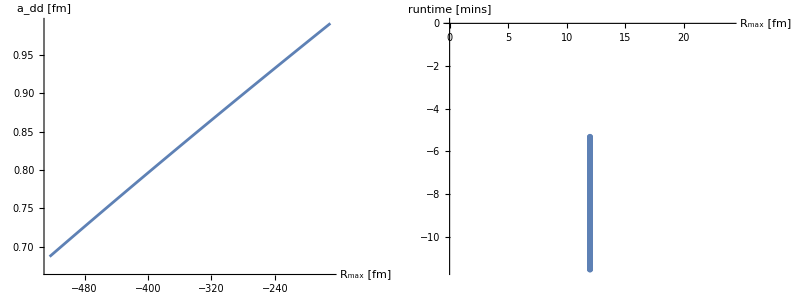

```mathematica
rMaxStart=15;
rMaxEnd=20;
nbrR=1;
coreNBR=1;
{e0Core,dimerCore}={-2.11778,{{0.130488,0.083336},{0.362742,0.52831},{0.733886,2.7561},{0.559288,8.8158}}};
RmaxRange=Range[rMaxStart,rMaxEnd,N[(rMaxEnd-rMaxStart)/nbrR]];
energ=0.001;
grdPerFermi=12;
numRAD=9;
results={};
resultsWF={};
results1={};
runtimes={};
NormTF[dimerCore]
(*SetSharedVariable[results,resultsPhases];*)

Do[ LECd=nt;
nGrd=IntegerPart[rMa grdPerFermi];
ta=AbsoluteTime[];
{tmp,tmp2}=GetEREP3[lambdaTest,20,nGrd,dimerCore,LECc,LECd,energ,numRAD];.
tb=AbsoluteTime[];
AppendTo[results,tmp];
AppendTo[resultsWF,tmp2];
AppendTo[results1,nt];
AppendTo[runtimes,{rMa,(tb-ta)/60.}];
Print["core ",coreNBR,"| maxE=",numRAD," )  λ = ",lambdaTest,"   C_0(λ) = ",LECc,"   D_0(λ) = ",LECd,"     R_max = ",rMa,"     #(grid points) = ",nGrd,"                a_dd = ",tmp," fm        a_dd/a_aa = ",Style[tmp/(hbar/√(Mm Abs[e0Core])),Red,18]];
,{nt,Reverse[Range[-1250,-170]]}];
Grid[{{ListPlot[Transpose[{results1,results}],ImageSize->Large,Joined->True,AxesLabel->{"R_max [fm]","a_dd [fm]"}],ListPlot[runtimes,ImageSize->Large,AxesLabel->{"R_max [fm]","runtime [mins]"}]}}]
```

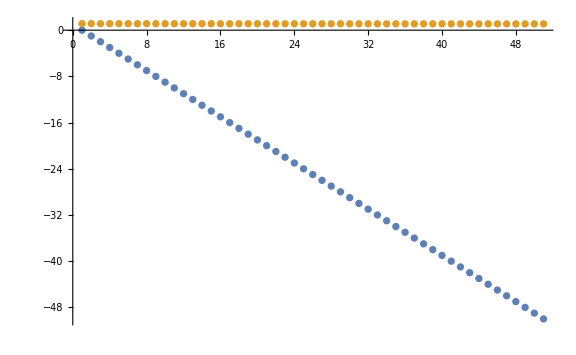

```mathematica
ListPlot[{results1,results},PlotRange->Full,ImageSize->Large]
```